```mathematica
ppp[t_]:=1/(1+a*t^2)
```

```mathematica
pp[t_]=Integrate[-ppp[t],t]-(Integrate[ppp[t],t]/.t->0)
```

-ArcTan[√a t]/(√a)

```mathematica
p[t_]=Integrate[-pp[t],t]-(Integrate[pp[t],t]/.t->1)
```

(ArcTan[√a]-Log[1+a]/(2 √a))/(√a)+(t ArcTan[√a t]-Log[1+a t^2]/(2 √a))/(√a)

```mathematica
p[1]
```

0

```mathematica
pp[0]
```

0

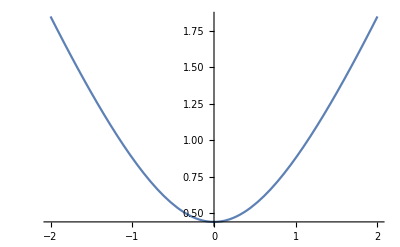

```mathematica
Plot[p[t]/.a->1,{t,-2,2}]
```

```mathematica
y[t_]=48*Integrate[p[t],t]
```

-(24 (-t-2 √a t ArcTan[√a]+ArcTan[√a t]/(√a)-√a t^2 ArcTan[√a t]+t Log[1+a]+t Log[1+a t^2]))/a

```mathematica
y[0]
```

0

```mathematica
x[t_] = Integrate[y[t],t]
```

1/a^(3/2)24 (-1/6 √a t^2+a t^2 ArcTan[√a]+1/3 t (-3+a t^2) ArcTan[√a t]+(2 Log[1+a t^2])/(3 √a)-1/2 √a (-t^2-t^2 (1-Log[1+a])+((1+a t^2) Log[1+a t^2])/a))

```mathematica
A=x[1]//Simplify
```

(4 (5 a+2 √a (-3+4 a) ArcTan[√a]+(1-6 a) Log[1+a]))/a^2

```mathematica
x[t]-A//Simplify
```

1/a^2 4 (-5 a+5 a t^2+2 √a (3+a (-4+3 t^2)) ArcTan[√a]+2 √a t (-3+a t^2) ArcTan[√a t]-Log[1+a]+6 a Log[1+a]-3 a t^2 Log[1+a]+Log[1+a t^2]-3 a t^2 Log[1+a t^2])

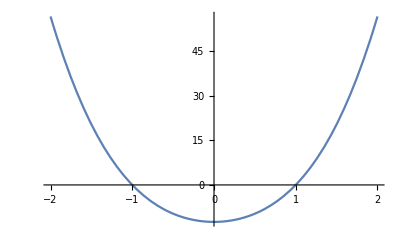

```mathematica
Plot[x[t]-A/.a->1,{t,-2,2}]
```

```mathematica
x[1]
```

-10